## LeNet and MNIST

```mathematica
from: https://reference.wolfram.com/language/tutorial/NeuralNetworksIntroduction.html#621730217
```

```mathematica
trainingData = ResourceData["MNIST", "TrainingData"];
testData = ResourceData["MNIST", "TestData"];
```

```mathematica
randomSample = RandomSample[trainingData, 5]
```

{-Graphics-→6,-Graphics-→4,-Graphics-→3,-Graphics-→1,-Graphics-→4}

```mathematica
lenetModel = NetModel["LeNet Trained on MNIST Data"]
```

NetChain[<>]

```mathematica
lenetModel[{-Graphics-, -Graphics-, -Graphics-, -Graphics-}]
```

{3,9,8,4}

```mathematica
NetTrain[NetModel["LeNet"], trainingData, ValidationSet->testData]
```

NetChain[<>]

## Layers

```mathematica
lenetModel
```

NetChain[<>]

```mathematica
layer=NetExtract[lenetModel,-1]
```

SoftmaxLayer[<>]

```mathematica
layer[{1,2,5,2,4,7,4,3,5,3}]
```

{0.00174213,0.00473559,0.0951169,0.00473559,0.0349916,0.702824,0.0349916,0.0128727,0.0951169,0.0128727}

```mathematica
layer[NumericArray[{1.,2.,5.,2.,4.,7.,4.,3.,5.,3.},"Real32"]]
```

NumericArray[…]

```mathematica
Normal[%]
```

{0.00174213,0.00473559,0.0951169,0.00473559,0.0349916,0.702824,0.0349916,0.0128727,0.0951169,0.0128727}

```mathematica
Total[%]
```

1.

#### Construct a new layer

```mathematica
linear = LinearLayer[3,"Input"->2]
```

LinearLayer[<>]

```mathematica
linear[{2,3}]
```

LinearLayer::nninit: Cannot evaluate net: unspecified value for array "Weights".

$Failed

```mathematica
initializedLinear = NetInitialize[linear]
```

LinearLayer[<>]

```mathematica
initializedLinear[{2,3}]
```

{-1.59581,-1.79372,-1.96823}

```mathematica
NetExtract[initializedLinear, "Weights"]
```

NumericArray[…]

```mathematica
NetExtract[initializedLinear, "Biases"]
```

NumericArray[…]

```mathematica
Normal@%
```

{0.,0.,0.}

```mathematica
msloss=MeanSquaredLossLayer[]
```

MeanSquaredLossLayer[<>]

```mathematica
msloss[<|"Input"-> {1,2,3}, "Target"-> {4,0,4}|>]
```

4.66667

```mathematica
?*Layer
```

### NetEncoders

A net encoder that produces a 1x12x12 array:

```mathematica
imageenc = NetEncoder[{"Image", {12, 12}, "ColorSpace"-> "Grayscale"}]
```

NetEncoder[<>]

```mathematica
imageenc[-Graphics-] // Normal
```

{{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,0.,0.,0.,0.,0.,1.,1.,1.},{1.,1.,1.,0.,0.,0.,0.,0.,0.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,0.,0.,0.,1.,1.,1.},{1.,1.,1.,1.,0.,0.,0.,0.,0.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,1.,1.},{1.,1.,0.,1.,1.,1.,1.,1.,0.,0.,1.,1.},{1.,1.,0.,0.,1.,1.,0.,0.,0.,1.,1.,1.},{1.,1.,1.,1.,0.,0.,0.,0.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}}

```mathematica
img = -Graphics-; ImageDimensions[img]
```

{150,155}

```mathematica
imageenc[img]//Dimensions
```

{1,12,12}

While encoders can be used independently from nets, as we have done, it is more common to attach the encoder to a layer.This can be done when creating the layer or afterward.Here is an example of creating a layer with an attached encoder.

```mathematica
pool = PoolingLayer[10,"Input"->NetEncoder[{"Image",64}]]
```

PoolingLayer[<>]

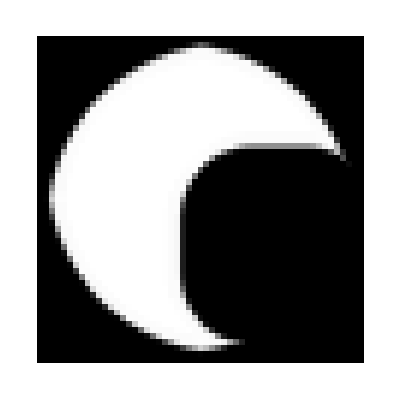
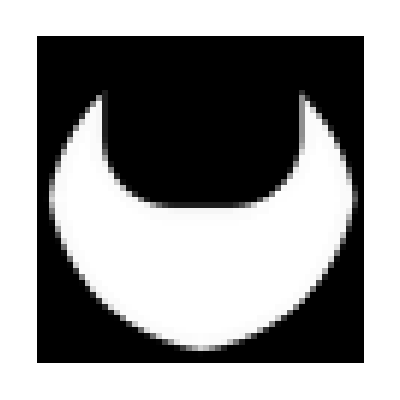
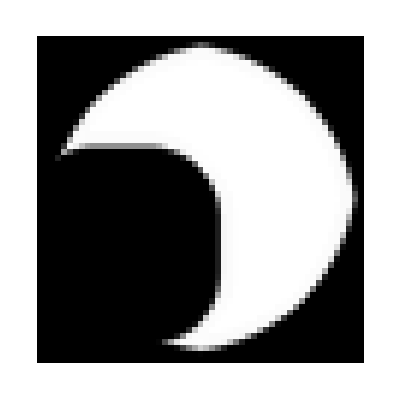

```mathematica
ArrayPlot /@ pool[-Graphics-]
```

```mathematica
Image[pool[-Graphics-], Interleaving -> False]
```

-Graphics-

Create an encoder for MNIST images

```mathematica
mnistEncoder = NetEncoder[{"Image",{28,28},"ColorSpace"-> "Grayscale"}]
```

NetEncoder[<>]

```mathematica
trainingData[[1,1]]
```

-Graphics-

```mathematica
ImageDimensions[%]
```

{28,28}

And a decoder

```mathematica
mnistDecoder = NetDecoder[{"Class", Range[0,9]}]
```

NetDecoder[<>]

By default, the decoder will decode a probability vector as a most likely class.

```mathematica
mnistDecoder[{0,0,0,1,0,0,0,0,0,0}]
```

3

Obtain the probability of a specific class:

```mathematica
mnistDecoder[{0,0,.3,.3,.3,.1,0,0,0,0}, {"Probability", 2}]
```

0.3

Obtain the full list of the probabilities as an association:

```mathematica
mnistDecoder[{0,0,.3,.3,.3,.1,0,0,0,0},"Probabilities"]
```

<|0→0.,1→0.,2→0.3,3→0.3,4→0.3,5→0.1,6→0.,7→0.,8→0.,9→0.|>

Obtain a measure of the certainty of the prediction:

```mathematica
mnistDecoder[{0,0,.3,.3,.3,.1,0,0,0,0},"Entropy"]
```

1.31383

Attach both a NetEncoder and a NetDecoder to a layer:

```mathematica
pool = PoolingLayer[10, "Input"->NetEncoder[{"Image",64}], "Output"-> NetDecoder["Image"]]
```

PoolingLayer[<>]

```mathematica
pool[-Graphics-]
```

-Graphics-

### Containers

Create a simple NetChain computing Cos[Sin[x]]:

```mathematica
chain = NetChain[{ElementwiseLayer[Sin],ElementwiseLayer[Cos]}]
```

NetChain[<>]

Apply to an input and compare to result of functions directly

```mathematica
inData = {3.2, -2.3};
chain[inData]
```

{0.998297,0.73461}

```mathematica
Cos[Sin[inData]]
```

{0.998297,0.73461}

Create a simple NetChain that consists of an ElementwiseLayer the applies the Ramp function, followed by a SoftmaxLayer:

```mathematica
layer1 = ElementwiseLayer[Ramp];
layer2 = SoftmaxLayer[];
chain = NetChain[{layer1, layer2}]
```

NetChain[<>]

```mathematica
inData1 = {-1, 3, 2, 4};
chain[inData1]
```

{0.0120376,0.241783,0.0889468,0.657233}

```mathematica
layer1[inData1]
```

{0.,3.,2.,4.}

```mathematica
layer2[%]
```

{0.0120376,0.241783,0.0889468,0.657233}